```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Mean@LogNormalDistribution[μ,σ]
```

ⅇ^(μ+σ^2/2)

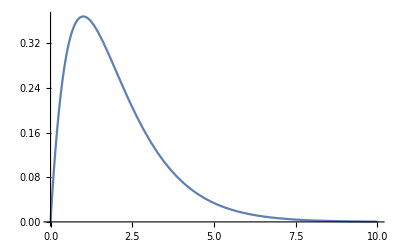

```mathematica
Plot[PDF[GammaDistribution[2,1],x],{x,0,10}]
```

```mathematica
NIntegrate[PDF[GammaDistribution[2,1],d]*Likelihood[LogNormalDistribution[d,1],{3.3,1,0.5,0.4,3.3}],{d,0,1000}]
```

0.000102041

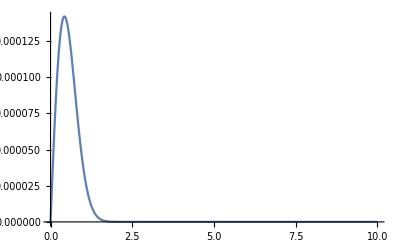

```mathematica
Plot[PDF[GammaDistribution[2,1],d]*Likelihood[LogNormalDistribution[d,1],{3.3,1,0.5,0.4,3.3}],{d,0,10},PlotRange->Full]
```

```mathematica
NSolve[{D[Simplify[Likelihood[LogNormalDistribution[d,1],{3.3,1,0.5,0.4,3.3}]*PDF[GammaDistribution[2,1],d],d>0],d]==0,d>0},d]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{d→0.425603}}

```mathematica
Simplify[PDF[GammaDistribution[2,1],d]*Likelihood[LogNormalDistribution[d,1],{3.3,1,0.5,0.4,3.3}],d>0]
```

0.000576479 d ⅇ^(-0.221593 d-2.5 d^2)